Took ~1 min to rerun this notebook on my laptop

### Smore Model 1: Sandwich blocks (1D)

```mathematica
r1 = 5/1000; r3 = 2/100; sideLength =3*2.54/100
thickMarsh = th /. Solve[Pi*0.04*(r3^2-r1^2) == sideLength^2th, th][[1]]
```

0.0762

0.0081158

```mathematica
thickChoc = 0.005; thickGram = 2.54/100/8;
boundMarsh = thickMarsh/2; boundChoc = boundMarsh + thickChoc; boundTotal= boundChoc + thickGram
 hAir = 10; TempAir = 25; TempInit = 25; TempMarshInit = 186;
```

0.0122329

```mathematica
ρ[x_] :=Piecewise[{
{400, Abs[x]<=boundMarsh},
{1250, boundMarsh< Abs[x]<= boundChoc},
{500,  boundChoc < Abs[x]<= boundTotal}
}] 
k[x_]:=Piecewise[{
{0.05, Abs[x]<=boundMarsh},
{0.3, boundMarsh< Abs[x]<= boundChoc},
{0.01,  boundChoc < Abs[x]<= boundTotal}
}] 
cpBase[x_]:=Piecewise[{
{2000, Abs[x]<=boundMarsh},
{1800, boundMarsh< Abs[x]<= boundChoc}, (*could further complicate by making this incr +10 per deg*)
{5000,  boundChoc < Abs[x] <= boundTotal}
}] 
α[x_]:=k[x]/(ρ[x]*cpBase[x])
```

```mathematica
Theta[t_,x_]:= 1/2(Erf[(boundMarsh-x)/(2Sqrt[α[x]t])]+Erf[(boundMarsh+x)/(2Sqrt[α[x]t])])
sandwichTemp[t_,x_]:=TempInit + (TempMarshInit-TempInit)*Theta[t,x]
```

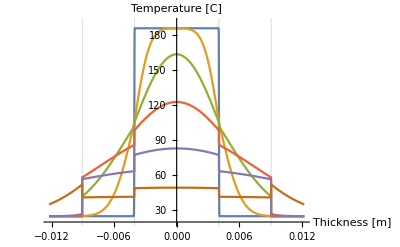

```mathematica
Plot[{sandwichTemp[0.001, x], sandwichTemp[10, x], sandwichTemp[60, x],sandwichTemp[180, x],sandwichTemp[600, x],sandwichTemp[3600, x]},{x,-boundTotal,boundTotal}, 
PlotRange -> {{-boundTotal,boundTotal},{TempAir-5,TempMarshInit+5}},
GridLines->{{boundMarsh,boundChoc, -boundMarsh,-boundChoc},{}},
AxesLabel->{"Thickness [m]", "Temperature [C]"}
]
```

```mathematica
Manipulate[
Plot[sandwichTemp[t, x],{x,-boundTotal,boundTotal}, 
PlotRange -> {{-boundTotal,boundTotal},{TempAir-5,TempMarshInit+5}},
Filling->Bottom,
GridLines->{{boundMarsh,boundChoc, -boundMarsh,-boundChoc},{}},
AxesLabel->{"Thickness [m]", "Temperature [C]"}
],
{{t, 0.001, "Time"}, 0.001, 600, 1}
]
```

### Smore Model 2: FEM heat transfer (3D)

```mathematica
Needs["NDSolve`FEM`"]
gridFine = 2*10^-9;
smore = Cuboid[{-boundTotal,-sideLength/2, -sideLength/2},{boundTotal,sideLength/2, sideLength/2}];
smoreMesh = ToElementMesh[smore,"MaxCellMeasure"->gridFine,"MeshOrder"->1]
smoreMesh["Wireframe"]
```

ElementMesh[{{-0.0122329,0.0122329},{-0.0381,0.0381},{-0.0381,0.0381}},{HexahedronElement[<74420>]}]

-Graphics3D-

```mathematica
smoreGraphic = Graphics3D[{
Yellow,
Cuboid[{-boundTotal,-sideLength/2, -sideLength/2},{-boundChoc,sideLength/2, sideLength/2}],
Cuboid[{boundTotal,-sideLength/2, -sideLength/2},{boundChoc,sideLength/2, sideLength/2}],
Darker[Brown],
Cuboid[{-boundChoc,-sideLength/2, -sideLength/2},{-boundMarsh,sideLength/2, sideLength/2}],
Cuboid[{boundChoc,-sideLength/2, -sideLength/2},{boundMarsh,sideLength/2, sideLength/2}],
White,
Cuboid[{-boundMarsh,-sideLength/2, -sideLength/2},{boundMarsh,sideLength/2, sideLength/2}]
}]
```

-Graphics3D-

```mathematica
pdeSmore3D= HeatTransferPDEComponent[{T[t,x, y,z],t,{x,y,z}},<|"MassDensity"->ρ[x],"ThermalConductivity"->{{k[x],0,0},{0,k[x], 0},{0,0, k[x]}},"SpecificHeatCapacity"->cpBase[x]|>]
```

({{-1. (Piecewise[{{0.05, Abs[x]≤0.0040579}, {0.3, 0.0040579<Abs[x]≤0.0090579}, {0.01, 0.0090579<Abs[x]≤0.0122329}, {0., True}}]),0.,0.},{0.,-1. (Piecewise[{{0.05, Abs[x]≤0.0040579}, {0.3, 0.0040579<Abs[x]≤0.0090579}, {0.01, 0.0090579<Abs[x]≤0.0122329}, {0., True}}]),0.},{0.,0.,-1. (Piecewise[{{0.05, Abs[x]≤0.0040579}, {0.3, 0.0040579<Abs[x]≤0.0090579}, {0.01, 0.0090579<Abs[x]≤0.0122329}, {0., True}}])}}.T[t,x,y,z]{x,y,z}Inactive){x,y,z}Inactive+(Piecewise[{{400., Abs[x]≤0.0040579}, {1250., 0.0040579<Abs[x]≤0.0090579}, {500., 0.0090579<Abs[x]≤0.0122329}, {0., True}}]) (Piecewise[{{2000., Abs[x]≤0.0040579}, {1800., 0.0040579<Abs[x]≤0.0090579}, {5000., 0.0090579<Abs[x]≤0.0122329}, {0., True}}]) T^(1,0,0,0)[t,x,y,z]

```mathematica
bcTempInit = T[0,x,y, z]==If[Abs[x]<= boundMarsh, TempMarshInit, TempInit];
bcConvX = NeumannValue[hAir(TempAir-T[t,x,y, z]),x== boundTotal];
bcConvY = NeumannValue[hAir(TempAir-T[t,x,y, z]),y== sideLength/2];
bcConvZ = NeumannValue[hAir(TempAir-T[t,x,y, z]),z== sideLength/2];
bcConvXN = NeumannValue[hAir(TempAir-T[t,x,y, z]),x== -boundTotal];
bcConvYN = NeumannValue[hAir(TempAir-T[t,x,y, z]),y== -sideLength/2];
bcConvZN = NeumannValue[hAir(TempAir-T[t,x,y, z]),z== -sideLength/2];
```

```mathematica
simulationTime = 600;
smoreHeat3D = NDSolveValue[{bcTempInit, pdeSmore3D==(bcConvX+bcConvY+bcConvZ)+(bcConvXN+bcConvYN+bcConvZN)},T,{t,0,simulationTime},{x,y,z} ∈ smoreMesh]
```

InterpolatingFunction[{{0., 600.}, {-0.0122329, 0.0122329}, {-0.0381, 0.0381}, {-0.0381, 0.0381}}, <>]

```mathematica
Manipulate[
Plot[{sandwichTemp[t,x],smoreHeat3D[t, x, 0,0]},{x,-boundTotal,boundTotal}, 
PlotRange -> {{-boundTotal,boundTotal},{TempAir-5, TempMarshInit+5}},
Filling->Bottom,
GridLines->{{boundMarsh,boundChoc, -boundMarsh,-boundChoc},{}},
AxesLabel->{"Thickness [m]", "Temperature [C]"},
PlotLegends->{"Sandwich Block Model", "FEM Model Simple"}
],
{{t, 0.001, "Time"}, 0.001, simulationTime, 1}
]
```

```mathematica
colorTempsSmore = ColorData["TemperatureMap"][Rescale[#,{TempAir,TempMarshInit}]]&;
Manipulate[
DensityPlot[smoreHeat3D[t, x, y,0],{x,-boundTotal,boundTotal},{y,-sideLength/2,sideLength/2}, 
ColorFunctionScaling-> False, ColorFunction->colorTempsSmore,
PlotLegends -> BarLegend[{colorTempsSmore, {TempAir, TempMarshInit}},LegendLabel->"T [deg C]"],
AspectRatio->2, FrameLabel->{Style["x [m]",Large], Style["y [m]",Large]},
PlotLabel->Style[StringForm["S'More Temp Profile \nat t = `` seconds",Round[t]],Large]
],
{{t, 0.001, "Time"}, 0.001, simulationTime, 1}
]
```

### Smore Model 3: FEM heat transfer + phase changes (1D)

```mathematica
(*HfMarsh= 2221000/.3423;TmMarsh = 186;*)
HfChoc = 31200; TmChoc = 33.1;
```

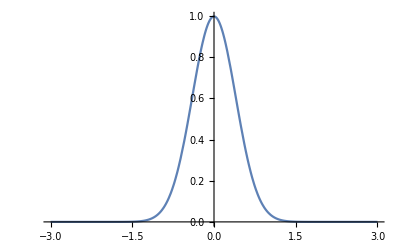

```mathematica
gauss[temp_, mean_, std_]:= PDF[ NormalDistribution[mean,std],temp]
Plot[gauss[x,0,0.4],{x,-3,3}]
cp[x_, temp_]:=Piecewise[{
{2000(*+HfMarsh*gauss[temp, TmMarsh,0.4]*), Abs[x]<=boundMarsh},
{1800+HfChoc*gauss[temp, TmChoc, 0.4], boundMarsh< Abs[x]<= boundChoc}, 
{5000,  boundChoc < Abs[x] <= boundTotal}
}]
```

```mathematica
smore1D = Line[{{-boundTotal},{boundTotal}}];
smoreMesh1D = ToElementMesh[smore1D,"MaxCellMeasure"->boundTotal/100,"MeshOrder"->1]
```

ElementMesh[{{-0.0122329,0.0122329}},{LineElement[<200>]}]

```mathematica
pdeSmore1D= HeatTransferPDEComponent[{T[t,x],t,{x}},<|"MassDensity"->ρ[x],"ThermalConductivity"->{{k[x]}},"SpecificHeatCapacity"->cp[x, T[t,x]]|>]
```

({{-1. (Piecewise[{{0.05, Abs[x]≤0.0040579}, {0.3, 0.0040579<Abs[x]≤0.0090579}, {0.01, 0.0090579<Abs[x]≤0.0122329}, {0., True}}])}}.T[t,x]{x}Inactive){x}Inactive+(Piecewise[{{400., Abs[x]≤0.0040579}, {1250., 0.0040579<Abs[x]≤0.0090579}, {500., 0.0090579<Abs[x]≤0.0122329}, {0., True}}]) (Piecewise[{{2000., Abs[x]≤0.0040579}, {1800.+31117.5 2.71828^(-3.125 (-33.1+T[t,x])^2), 0.0040579<Abs[x]≤0.0090579}, {5000., 0.0090579<Abs[x]≤0.0122329}, {0., True}}]) T^(1,0)[t,x]

```mathematica
bcTempInit1D = T[0,x]==If[Abs[x]<= boundMarsh, TempMarshInit, TempInit];
bcConvX1D = NeumannValue[hAir(TempAir-T[t,x]),x== boundTotal];
bcConvXN1D = NeumannValue[hAir(TempAir-T[t,x]),x== -boundTotal];
```

```mathematica
simulationTime = 600;
smoreHeat = NDSolveValue[{bcTempInit1D, pdeSmore1D==bcConvX1D+bcConvXN1D},T,{t,0,simulationTime},{x} ∈ smoreMesh1D]
```

InterpolatingFunction[{{0., 600.}, {-0.0122329, 0.0122329}}, <>]

```mathematica
Manipulate[
Plot[{sandwichTemp[t,x],smoreHeat3D[t, x, 0,0], smoreHeat[t,x]},{x,-boundTotal,boundTotal}, 
PlotRange -> {{-boundTotal,boundTotal},{TempAir-5, 200}},
Filling->Bottom,
PlotLabel->Style[StringForm["S'More Temp Profile \nat t = `` seconds",Round[t]],Large],
GridLines->{{{boundMarsh,Directive[Black]},{boundChoc,Directive[Black]},{-boundMarsh,Directive[Black]},{-boundChoc,Directive[Black]}},{}},
AxesLabel->{"x [m]", "T [deg C]"},
PlotLegends->{"Sandwich Block Model (1D)", "FEM Heat Transfer (3D)", "FEM Heat Transfer\n+ Phase Change (1D)"}
],
{{t, 0.001, "Time"}, 0.001, simulationTime, 1}
]
```